```mathematica
{x0,v0} = {-1,-2};
{xp0, vp0} = {v0, -4x0};
```

```mathematica
fordward[dt_,x0_,v0_] = Function[{dt, x0,v0},
{x0,v0}+ dt{v0,-4x0} ]
```

Function[{dt,x0,v0},{x0,v0}+dt {v0,-4 x0}]

```mathematica
dt =0.11;
hist2= {};
Do[{{x,v} = {x0,v0} + dt{xp0,vp0},
{x0,v0} = {x,v},
{xp0, vp0} = {v0, -4x0},AppendTo[hist2, {x,v}]},{i ,1,200}]
```

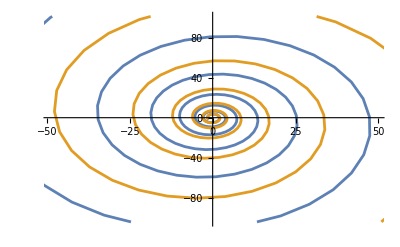

```mathematica
ListPlot[{hist1,hist2},Joined->True]
```

```mathematica
{x0,v0} = {-1,-2};
{xp0, vp0} = {v0, -4x0};
```

```mathematica
dt =0.1;
hist1 = {};
Do[{{x,v} = {x0,v0} + dt{({x0,v0}+dt{xp0,vp0})[[2]], -4({x0,v0}+dt{xp0,vp0})[[1]]},
{x0,v0} = {x,v},
{xp0, vp0} = {v0, -4x0},AppendTo[hist1, {x,v}]},{i ,1,200}]
```

```mathematica
dt =0.11;
hist2 = {};
Do[{{x,v} = {x0,v0} + dt{({x0,v0}+dt{xp0,vp0})[[2]], -4({x0,v0}+dt{xp0,vp0})[[1]]},
{x0,v0} = {x,v},
{xp0, vp0} = {v0, -4x0},AppendTo[hist2, {x,v}]},{i ,1,200}]
```

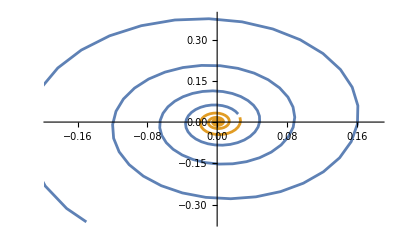

```mathematica
ListPlot[{hist1,hist2},Joined->True]
```

```mathematica
{x0,v0} = {-1,-2};
{xp0, vp0} = {v0, -4x0};
```

```mathematica
dt =0.1;
hist1 = {};
Do[{{x,v} = {x0,v0} + dt{({x0,v0}+dt{xp0,vp0})[[2]], -4({x0,v0}+dt{xp0,vp0})[[1]]},
{x0,v0} = {x,v},
{xp0, vp0} = {v0, -4x0},AppendTo[hist1, {x,v}]},{i ,1,200}]
```

```mathematica
dt =0.1;
hist2= {};
Do[{{x,v} = {x0,v0} + dt{xp0,vp0},
{x0,v0} = {x,v},
{xp0, vp0} = {v0, -4x0},AppendTo[hist2, {x,v}]},{i ,1,200}]
```

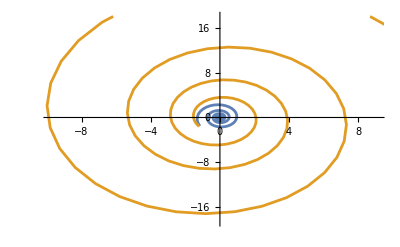

```mathematica
ListPlot[{hist1,hist2},Joined->True]
```

```mathematica
{x0,v0} = {-1,-2};
{xp0, vp0} = {v0, -2x0};
```

```mathematica
dt =0.05;
hist2= {};
Do[{{x,v} = {x0,v0} + dt{xp0,vp0},
{x0,v0} = {x,v},
{xp0, vp0} = {v0, -2x0},Print[dt*i, {x,v}]},{i ,1,51}]
```

0.05{-1.1,-1.9}

0.1{-1.195,-1.79}

0.15{-1.2845,-1.6705}

0.2{-1.36803,-1.54205}

0.25{-1.44513,-1.40525}

0.3{-1.51539,-1.26073}

0.35{-1.57843,-1.1092}

0.4{-1.63389,-0.951353}

0.45{-1.68145,-0.787964}

0.5{-1.72085,-0.619819}

0.55{-1.75184,-0.447734}

0.6{-1.77423,-0.27255}

0.65{-1.78786,-0.0951265}

0.7{-1.79261,0.0836592}

0.75{-1.78843,0.262921}

0.8{-1.77528,0.441764}

0.85{-1.7532,0.619292}

0.9{-1.72223,0.794612}

0.95{-1.6825,0.966835}

1.{-1.63416,1.13509}

1.05{-1.57741,1.2985}

1.1{-1.51248,1.45624}

1.15{-1.43967,1.60749}

1.2{-1.35929,1.75146}

1.25{-1.27172,1.88739}

1.3{-1.17735,2.01456}

1.35{-1.07662,2.13229}

1.4{-0.970009,2.23996}

1.45{-0.858011,2.33696}

1.5{-0.741163,2.42276}

1.55{-0.620026,2.49687}

1.6{-0.495182,2.55888}

1.65{-0.367238,2.60839}

1.7{-0.236818,2.64512}

1.75{-0.104562,2.6688}

1.8{0.0288776,2.67926}

1.85{0.16284,2.67637}

1.9{0.296659,2.66008}

1.95{0.429663,2.63042}

2.{0.561184,2.58745}

2.05{0.690557,2.53133}

2.1{0.817123,2.46228}

2.15{0.940237,2.38057}

2.2{1.05927,2.28654}

2.25{1.17359,2.18062}

2.3{1.28262,2.06326}

2.35{1.38579,1.93499}

2.4{1.48254,1.79642}

2.45{1.57236,1.64816}

2.5{1.65476,1.49093}

2.55{1.72931,1.32545}